```mathematica
(* 1 *)
PolynomialQuotientRemainder[x^3+2x^2 - 7, x  + 2, x] // TraditionalForm
```

{x^2,-7}

```mathematica
f[x_] := 5x^4+30x^3-40x^2+36x+14
f[-7]
```

-483

```mathematica
PolynomialQuotientRemainder[x^3 + 4*x^2 - 6*x + 2, x - 1, x]
```

```mathematica
{-1+5 x+x^2,1}
```

```mathematica
(x^2 + 5x  - 1)(x - 1) + 1 // Together // TraditionalForm
```

x^3+4 x^2-6 x+2

```mathematica
PolynomialQuotientRemainder[2x^3-3x^2-2x, 2x - 3, x]
```

{-1+x^2,-3}

```mathematica
(x^2-1)(2x-3) - 3//Together//TraditionalForm
```

2 x^3-3 x^2-2 x

```mathematica
PolynomialQuotientRemainder[4x^3+7x+9, 2x+1,x]//TraditionalForm
```

{2 x^2-x+4,5}

```mathematica
(2x^2 - x + 4)(2x+1) + 5 //Together//TraditionalForm
```

4 x^3+7 x+9

```mathematica
PolynomialQuotientRemainder[x^3+6x+3,x^2-2x+2,x]//TraditionalForm
```

{x+2,8 x-1}

```mathematica
2x - 1/2- 15/(2(2x-1)) // Together//TraditionalForm
```

(4 x^2-3 x-7)/(2 x-1)

```mathematica
(x+2)x(x-2)(x-4)//Expand//TraditionalForm
```

x^4-4 x^3-4 x^2+16 x

```mathematica
(x+1)(x-1)(x-3)//Expand//TraditionalForm
```

x^3-3 x^2-x+3

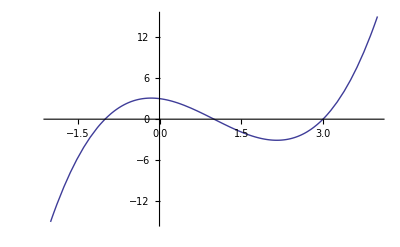

```mathematica
Plot[3-x-3 x^2+x^3,{x,-2.,4}]
```

```mathematica
x^3 - 3x^2 -x+3
```

3-x-3 x^2+x^3

```mathematica
Factor[3-x-3 x^2+x^3]
```

(-3+x) (-1+x) (1+x)

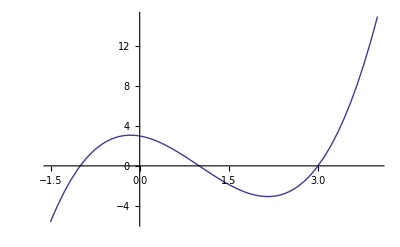

```mathematica
(-3+x) (-1+x) (1+x),{x,-
```

```mathematica
x^4 - 4x^3 -4x^2 // Factor
```

x^2 (-4-4 x+x^2)

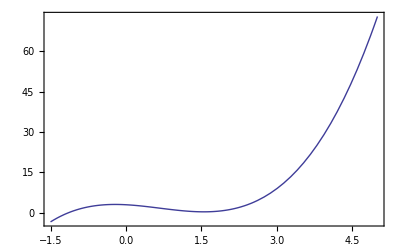

```mathematica
Show[%24,Frame->True,FrameStyle->Black]
```

```mathematica
x(x+2)(x-2)(x-4)//Expand//TraditionalForm
```

x^4-4 x^3-4 x^2+16 x

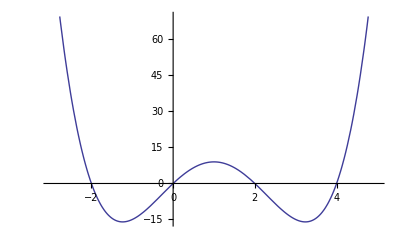

```mathematica
Plot[16 x-4 x^2-4 x^3+x^4,{x,-3.,5.}]
```

```mathematica
(x+1)(x-1)(x-2)//Expand//TraditionalForm
```

x^3-2 x^2-x+2

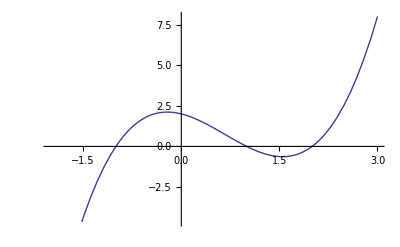

```mathematica
Plot[2-x-2 x^2+x^3,{x,-2.,3.}]
```

```mathematica
(x+1)(x-2)^2//Expand//TraditionalForm
```

x^3-3 x^2+4

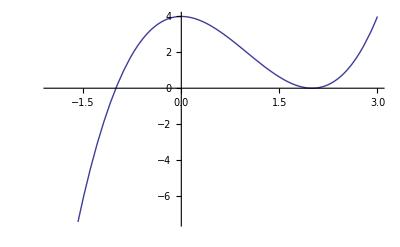

```mathematica
Plot[4-3 x^2+x^3,{x,-2.,3.}]
```

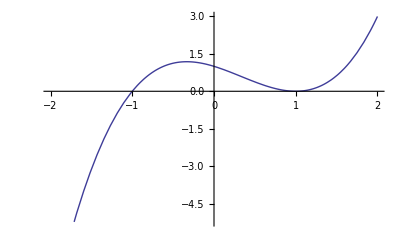

```mathematica
Plot[1-x-x^2+x^3,{x,-2.,2.}]
```

```mathematica
PolynomialRemainder[x^567 - 3x^400 + x^9 + 2, x-1,x]
```

1

```mathematica
f[x_]=(2x)/(x-1);
g[x_]=3x+1;
fg=f[g[x]];
gf=g[f[x]];
ff =f[f[x]];
gg=g[g[x]];

functions={fg,gf,ff,gg};

TableForm[Map[List[#//TraditionalForm,#//Together//ExpandNumerator//ExpandDenominator//TraditionalForm]&, functions],{TableAlignments->Right}]
```

(2 (3 x+1))/(3 x) | (6 x+2)/(3 x)
(6 x)/(x-1)+1 | (7 x-1)/(x-1)
(4 x)/((x-1) ((2 x)/(x-1)-1)) | (4 x)/(x+1)
3 (3 x+1)+1 | 9 x+4

```mathematica
(x+1)(x-2)^2//Expand//TraditionalForm
```

x^3-3 x^2+4

```mathematica
(x+2t)^3//Expand//TraditionalForm
```

8 t^3+12 t^2 x+6 t x^2+x^3